```mathematica
Three Wave Mixing in Fourier Space
```

```mathematica
"We are looking at Three Wave Mixing in a 2D System.The PDEs we use are the Manley Rowe Relations applied to Fourier Series describing the input and output fields.These inputs are a discrete Gaussian distribution of three Fourier modes each for waves 1 and 2 and a zero input for wave three. The solutions of the equations are the coefficients of the Fourier modes.These coefficients are a function of z (distance of propagation)."
```

```mathematica
np=2;xmax=10; zmax=100;
X2=0.10; cl=1;
w1=5; w2=6; w3=w1+w2;
n1=1.500;n2=1.500;n3=1.600; 
k1=w1 n1/cl; k2=w2 n2/cl; k3=w3 n3/cl; dk=k3-k2-k1

lowA=4;
Av=Table[a[i+lowA,z],{i,1,np}];
Av0=Table[a[i+lowA,0]==Exp[-(i-(np/2+0.5))^2],{i,1,np}];
Ak=Table[(i+lowA) 2 Pi/xmax,{i,1,np}];

lowB=5;
Bv=Table[b[i+lowB,z],{i,1,np}];
Bv0=Table[b[i+lowB,0]==Exp[-(i-(np/2+0.5))^2],{i,1,np}];
Bk=Table[(i+lowB) 2 Pi/xmax,{i,1,np}];

Cv=Table[c[i+lowA+lowB+1,z],{i,1,2 np-1}];
Cv0=Table[c[i+lowA+lowB+1,0]== 0 Exp[-(i-(np))^2],{i,1,2 np-1}];
Ck=Table[(i+lowA+lowB+1) 2 Pi/xmax,{i,1,2 np-1}];

eq1=I k1 D[Av,z]==1/2 Ak^2 Av-X2 w1^2/cl^2 Exp[-I dk z]ListConvolve[Reverse[Bv*],Cv];
eq2=I k2 D[Bv,z]==1/2 Bk^2 Bv-X2 w2^2/cl^2 Exp[-I dk z]ListConvolve[Reverse[Av*],Cv];
eq3=I k3 D[Cv,z]==1/2 Ck^2 Cv-X2 w3^2/cl^2 Exp[I dk z] ListConvolve[Av,Bv,{1,-1},0];

sol=NDSolve[{eq1,eq2,eq3,Av0,Bv0,Cv0},Join[Av,Bv,Cv],{z,0,zmax},  MaxStepSize->0.0001][[1]];
```

1.1

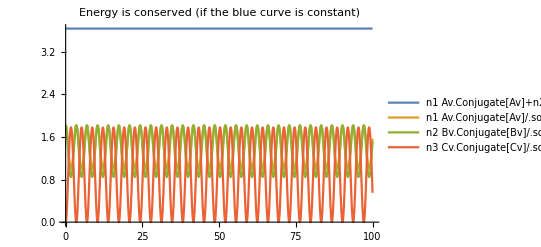

```mathematica
Plot[{ReplaceAll[n1 Av. Conjugate[Av]+n2 Bv. Conjugate[Bv]+n3 Cv. Conjugate[Cv], sol],n1 Av. Conjugate[Av]/.sol,n2 Bv. Conjugate[Bv]/.sol,n3 Cv. Conjugate[Cv]/.sol}, {z, 0,zmax}, PlotLegends->"Expressions",PlotLabel->"Energy is conserved (if the blue curve is constant)"]
```

```mathematica
StandardDeviation[Arg[Av0[[All,2]]]-Arg[Av]]/.sol/.z->1
Arg[Bv0[[All,2]]]-Arg[Bv]/.sol/.z->1
Arg[Cv0[[All,2]]]-Arg[Cv]/.sol/.z->1
```

0.205412

{0.703352,0.988854}

{-0.717761,-0.445989,-0.162192}

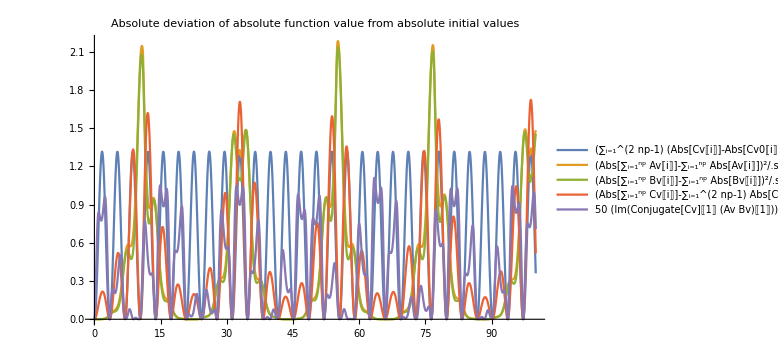

```mathematica
Plot[{(Sum[(Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]])^2,{i,1,2np-1}]/.sol)+(Sum[(Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]])^2,{i,1,np}]/.sol)+(Sum[(Abs[Av[[i]]]-Abs[Av0[[i]][[2]]])^2,{i,1,np}]/.sol),(Abs[Sum[Av[[i]], {i,1,np}]]-Sum[Abs[Av[[i]]], {i,1,np}])^2/.sol, (Abs[Sum[Bv[[i]], {i,1,np}]]-Sum[Abs[Bv[[i]]], {i,1,np}])^2/.sol,(Abs[Sum[Cv[[i]], {i,1,np}]]-Sum[Abs[Cv[[i]]], {i,1,2np-1}])^2/.sol, 50 Im[Cv*[[1]] (Av Bv)[[1]]]^2/.sol },{z,0,zmax},PlotPoints->100, PlotRange->All, PlotLabel->"Absolute deviation of absolute function value from absolute initial values",  PlotLegends->"Expressions", ImageSize->Large]
```

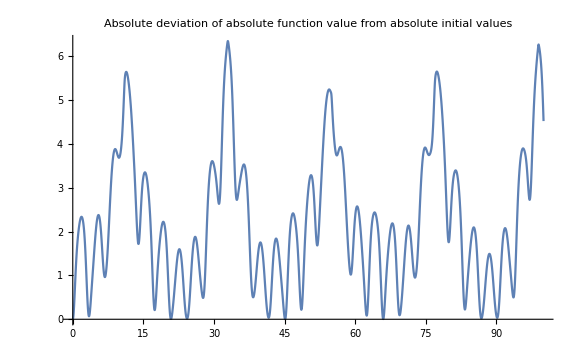

```mathematica
Plot[{(Sum[(Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]])^2,{i,1,2np-1}]/.sol)+(Sum[(Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]])^2,{i,1,np}]/.sol)+(Sum[(Abs[Av[[i]]]-Abs[Av0[[i]][[2]]])^2,{i,1,np}]/.sol)+((Abs[Sum[Av[[i]], {i,1,np}]]-Sum[Abs[Av[[i]]], {i,1,np}])^2/.sol)+( (Abs[Sum[Bv[[i]], {i,1,np}]]-Sum[Abs[Bv[[i]]], {i,1,np}])^2/.sol)+((Abs[Sum[Cv[[i]], {i,1,np}]]-Sum[Abs[Cv[[i]]], {i,1,2np-1}])^2/.sol)+ (50 (Im[Cv*[[1]] (Av Bv)[[1]]])^2/.sol) },{z,0,zmax},PlotPoints->100, PlotRange->Full, PlotLabel->"Absolute deviation of absolute function value from absolute initial values",  PlotLegends->"Expressions", ImageSize->Large]
```

```mathematica
zero=FindRoot[(Sum[(Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]])^2,{i,1,2np-1}]/.sol)+(Sum[(Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]])^2,{i,1,np}]/.sol)+(Sum[(Abs[Av[[i]]]-Abs[Av0[[i]][[2]]])^2,{i,1,np}]/.sol)+((Abs[Sum[Av[[i]], {i,1,np}]]-Sum[Abs[Av[[i]]], {i,1,np}])^2/.sol)+( (Abs[Sum[Bv[[i]], {i,1,np}]]-Sum[Abs[Bv[[i]]], {i,1,np}])^2/.sol)+((Abs[Sum[Cv[[i]], {i,1,np}]]-Sum[Abs[Cv[[i]]], {i,1,2np-1}])^2/.sol)+ (50 (Im[Cv*[[1]] (Av Bv)[[1]]])^2/.sol),{z,65}]
```

InterpolatingFunction::dmval: Input value {332.169} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{z→65.9436}

```mathematica
(Sum[(Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]])^2,{i,1,2np-1}]/.sol)+(Sum[(Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]])^2,{i,1,np}]/.sol)+(Sum[(Abs[Av[[i]]]-Abs[Av0[[i]][[2]]])^2,{i,1,np}]/.sol)+((Abs[Sum[Av[[i]], {i,1,np}]]-Sum[Abs[Av[[i]]], {i,1,np}])^2/.sol)+( (Abs[Sum[Bv[[i]], {i,1,np}]]-Sum[Abs[Bv[[i]]], {i,1,np}])^2/.sol)+((Abs[Sum[Cv[[i]], {i,1,np}]]-Sum[Abs[Cv[[i]]], {i,1,2np-1}])^2/.sol)+ (50 (Im[Cv*[[1]] (Av Bv)[[1]]])^2/.sol)/.zero
```

0.00606299

```mathematica
Abs[{Av,Bv,Cv}]/.sol/.zero
Arg[{Av,Bv,Cv}]/.sol/.zero
```

{{0.778834,0.777901},{0.777531,0.77903},{0.0387916,0.0167438,0.0315671}}

{{-0.543408,-0.550335},{1.36455,1.36144},{0.96743,-1.03654,-1.33459}}

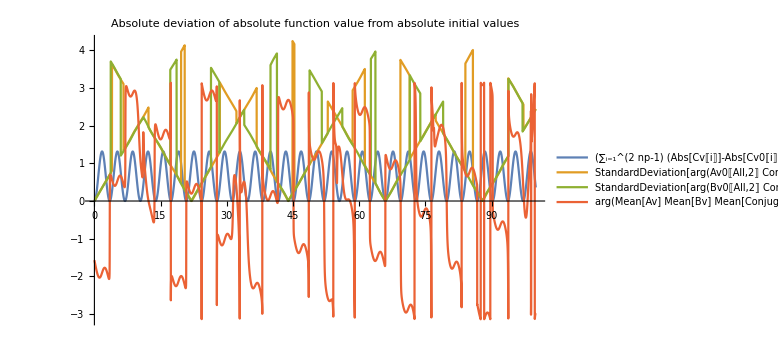

```mathematica
Plot[{(Sum[(Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]])^2,{i,1,2np-1}]/.sol)+(Sum[(Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]])^2,{i,1,np}]/.sol)+(Sum[(Abs[Av[[i]]]-Abs[Av0[[i]][[2]]])^2,{i,1,np}]/.sol),StandardDeviation[Arg[Av0[[All,2]]Av*]]/.sol,
StandardDeviation[Arg[Bv0[[All,2]]Bv*]]/.sol,Arg[Mean[Av]Mean[Bv] Mean[Cv*]]/.sol},{z,0,zmax},PlotPoints->100, PlotRange->All, PlotLabel->"Absolute deviation of absolute function value from absolute initial values",  PlotLegends->"Expressions", ImageSize->Large]
```

```mathematica
"Plot[{Evaluate[Table[Abs[a[lowA+i,z]]/.sol,{i,1 , np}]]}, {z, 0, zmax}, PlotLegends→Table[a[lowA+i,z],{i,np}], PlotLabel→"Evolution of modes in Subscript[E, 1]"]
Plot[{Evaluate[Table[Re[b[lowB+i,z]]/.sol,{i,1 , np}]]}, {z, 0, zmax}, PlotLegends→Table[b[lowB+i,z],{i,np}], PlotLabel→"Evolution of modes in Subscript[E, 2]"]
Plot[{Evaluate[Table[Re[c[lowA+lowB+1+i,z]]/.sol,{i,1 , 2 np-1}]]}, {z, 0, zmax}, PlotLegends→Table[c[lowA+lowB+1+i,z],{i,2np-1}], PlotLabel→"Evolution of modes in Subscript[E, 3]"]";
```

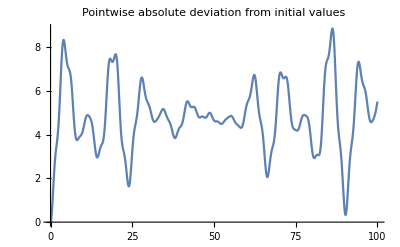

```mathematica
Plot[(Sum[Abs[Cv[[i]]-Cv0[[i]][[2]]]^2,{i,1,2np-1}]/.sol)+(Sum[Abs[Av[[i]]-Av0[[i]][[2]]]^2,{i,1, np}]/.sol)+(Sum[Abs[Bv[[i]]-Bv0[[i]][[2]]]^2,{i,1, np}]/.sol),{z,0,zmax},PlotPoints->200, PlotRange->Full, PlotLabel->"Pointwise absolute deviation from initial values"]
```

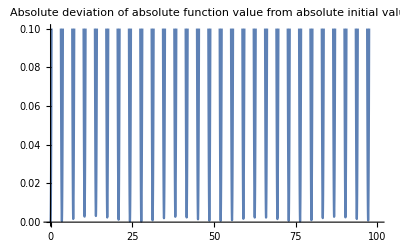

```mathematica
Plot[Abs[(Sum[Abs[Abs[Cv[[i]]]-Abs[Cv0[[i]][[2]]]]^2,{i,1,2np-1}]/.sol)]+Abs[(Sum[Abs[Abs[Bv[[i]]]-Abs[Bv0[[i]][[2]]]]^2,{i,1,np}]/.sol)]+Abs[(Sum[Abs[Abs[Av[[i]]]-Abs[Av0[[i]][[2]]]]^2,{i,1,np}]/.sol)],{z,0,zmax},PlotPoints->100, PlotRange->{Full, {0,0.1}}, PlotLabel->"Absolute deviation of absolute function value from absolute initial values"]
```

```mathematica
"Plot[{Evaluate[Table[Re[a[lowA+i,z]]/.sol,{i,1 , np}]],Evaluate[Table[Im[a[lowA+i,z]]/.sol,{i,1 , np}]]}, {z, 0, zmax}, PlotLegends→"Expressions", PlotLabel→"Evolution of modes in Subscript[E, 1]", ImageSize→Full]";
```